f(n) = n - f(f(n - 2))

```mathematica
f[n_]:=f[n]=n-f[f[n-1]]
f[1]=1;f[2]=1;
```

```mathematica
f[5]
```

3

```mathematica
Table[f[i], {i, 100}]
```

{1,1,2,3,3,4,4,5,6,6,7,8,8,9,9,10,11,11,12,12,13,14,14,15,16,16,17,17,18,19,19,20,21,21,22,22,23,24,24,25,25,26,27,27,28,29,29,30,30,31,32,32,33,33,34,35,35,36,37,37,38,38,39,40,40,41,42,42,43,43,44,45,45,46,46,47,48,48,49,50,50,51,51,52,53,53,54,55,55,56,56,57,58,58,59,59,60,61,61,62}

```mathematica
N[1-GoldenRatio]
```

-0.618034

```mathematica
N[1/GoldenRatio]
```

0.618034

lim as x goes to infinity, f[x] goes to 1-goldenRatio

```mathematica
a-f[f[a-2]]
a-a-f[f[f[a-f[f[a-2]]]]-2]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

a-TerminatedEvaluation[RecursionLimit]

```mathematica
a-f[f[a-2]]=1-f[Infinity]
```

```mathematica
g[x_]:=If[Mod[x, 2]==1, 3x+1, x/2]
g2[n_]:=Module[{i},
	i=n;
	While[g[i]!=1, i=g[i]];
	i
]
```

```mathematica
g2[6]
```

2

```mathematica
f1[n_]:=f1[n]=n/N[GoldenRatio]-f1[f1[n-1]]
f1[1]=1;f1[2]=1;
```

```mathematica
f1[5]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

3.09017-TerminatedEvaluation[RecursionLimit]

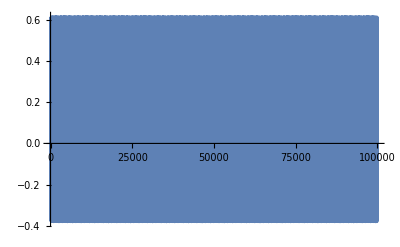

```mathematica
ListLinePlot[Table[f[n]-n/N[GoldenRatio], {n, 100000}], PlotRange->All]
```

```mathematica
n-a(a(n-2))==an
-a(a(n-2))=(a-1)n
2-n=((a-1)/n)/a^2
```

Let f[n] = an + b[x]

```mathematica
an+b[x]=x-
```

```mathematica
Collatz
```

```mathematica
Col=ResourceFunction["Collatz"]
```

```mathematica
Col[5]
```

{5,16,8,4,2,1}

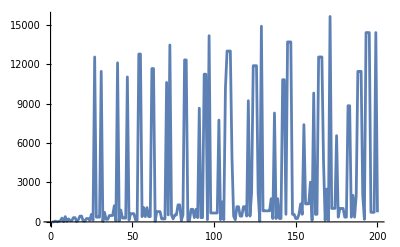

```mathematica
ListLinePlot[Table[Length[Col[i]]^2, {i, 200}], PlotRange->All]
```

```mathematica
Fib[x_]:=
```

```mathematica
f1[x_]:=n-f[f[n-2]]
f1[x_]:=n-n-f[f[f[n-n]-n]]
```

```mathematica
f1[n]:=n-f[x-2]-f[f[f[n-2]-2]]
```